```mathematica
Clear["Global`*"]
```

```mathematica
fun[x_] := x*Exp[-x]
```

```mathematica
fun[x]
```

ⅇ^-x x

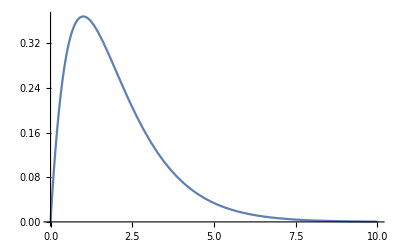

```mathematica
Plot[{fun[k]}, {k,-0,10}]
```

```mathematica
invfun[k_] := LaplaceTransform[fun[m],m,k]
```

```mathematica
invfun[x]
```

1/(1+x)^2

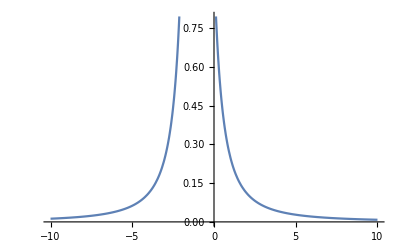

```mathematica
Plot[{invfun[k]}, {k,-10,10}]
```

```mathematica
lambda = 10^{-2};  b = 1 ; theta = 0.1 ; u = 0.5
c = lambda * (1+theta)* Integrate[per*fun[per], {per, 0, Infinity}]
```

0.5

{0.022}

```mathematica
phiinv[k_, c_, theta_, lambda_] := c * (theta/(1+theta)) / (c*k - lambda * (1 - invfun[k]))
```

```mathematica
phiinv[s, c, theta, lambda]
```

{0.002/(0.022 s+1/100 (-1+1/(1+s)^2))}

```mathematica
phi[w_]:= InverseLaplaceTransform[phiinv[s, c, theta, lambda], s, w]
```

```mathematica
phi[w]
```

{0.002 (500.+5.04602 ⅇ^(-1.4842 w)-459.591 ⅇ^(-0.0612511 w))}

```mathematica
psi[w_] := 1 - phi[w]
```

```mathematica
psi[w]
```

{1-0.002 (500.+5.04602 ⅇ^(-1.4842 w)-459.591 ⅇ^(-0.0612511 w))}

{0.886654}

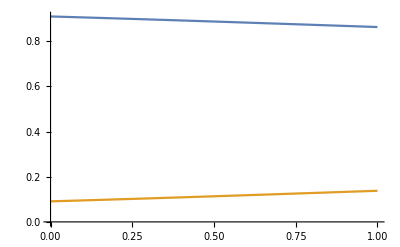

```mathematica
psi[0.5]
Plot[{psi[x], phi[x]}, {x, 0,1}]
```

```mathematica
bigx[z_, b_] := (1-psi[z]) / (1-psi[b])
```

```mathematica
bigx[1-z,1]
```

{0.0145226 (500.-432.286 ⅇ^(0.0612511 z)+1.14385 ⅇ^(1.4842 z))}

```mathematica
pofb := Integrate[bigx[b-x,b]*fun[x],  {x,0,b}]
```

```mathematica
pofb
```

{0.208276}

```mathematica
eud := bigx[u,b] * c/(lambda*(1-pofb))
```

```mathematica
eud
```

{2.28702}